# Mathematica Verification of SEGC_WL functions

## LJ_Module.lj

argon debroglie:

```mathematica
TLJ = 2;
h = 6.62607015×10^(-34);
kB = 1.380649×10^(−23);
mkg = 39.948*1.66054*10^(-27);
ϵ = 117.05*kB ;
TK = ϵ*TLJ/kB;
Λ=h/(√(2*π*mkg*kB*TK))
σA=3.4
(Λ*10^10)/3.4
```

1.80531×10^-11

3.4

0.0530973

E_12_frac_LJ:

```mathematica
ϕ[r_,λ_,M_]:=4* (λ/M)^(1/3)(((λ/M)^(1/4)/r )^12-((λ/M)^(1/4)/r)^6  )
rList={0.0001,1.0,2.0,10.0,30.0,5.6,100000000000.0};
rListSqrt=Sqrt[rList]
```

```mathematica
{0.01,1.,1.4142135623730951,3.1622776601683795,5.477225575051661,2.3664319132398464,316227.7660168379}
phiValues=ϕ[#,3,100]&/@rListSqrt
```

{0.01,1.,1.41421,3.16228,5.47723,2.36643,316228.}

{3.35581×10^19,-0.0064247,-0.000806758,-6.45823×10^-6,-2.39195×10^-7,-0.0000367738,-6.45826×10^-36}

## Physics test: Q(N=1|V,T) test

We have the partition function  which after solving the momenta integral becomes:
  . naturally the position coordinates are in  but following Desgranges and Allen and Tildesley, we want to rescale them to a unit box for ease of simulation thuse make the change of coordinates  so that now  lives in . From this transformation we get a factor of  for each particle. And thus we get the Desgranges expression of  for N=1, there are no interactions with other particles (and in our present situation no interactions with an external field) so  thus 

 which gives us our first test of the system wide physics. For L=8  , V = 512

```mathematica
V = 8^3
Λ = 0.07509097762269842 (*for argon_deBroglie at T*=1 *)
V/Λ^3
Log[V/Λ^3]
```

512

0.075091

1.20922×10^6

14.0055

So for our first physics Test  within some monte carlo sampling error

## Q(N=2|V,T) test

Although Q(N=2) cannot be solved for directly, we can indirectly find the analytic value for it using some thermodynamic relations in the infinite/large volume limit (or we could probably just numerically integrate it with a grid or quadrature for any volume). 

	First we define the mayer f-function: .  where u(rij) is the two particle interaction potential, which for us is the Lennard jones potential. Following R.K. Pathria and Paul D. Beale’s Third edition of Statistical Mechanics (2011) Chapter 10: Statistical Mechanics of Interacting Systems page 304: we look at the second cluster integral  and switch variables to integrate over  and :  recognizing that  and switching to a shell integral and integrating over the angular terms:  (eqn 10.1.18). Now technically this integral depends on V because r12 is bounded by the finite volume of the system, but if V is large, we can assume the mayer function decays to zero before the wall is reached and thus set our bounds of integration to be 0 and infinity. For the lennard jones system this can be analytically solved:

```mathematica
(*you have to restart the notebook kernel before running this for some reason*)
int=Integrate[r^2*(Exp[-4 (1/r^12-1/r^6)]-1),{r,0,Infinity}]
```

-1/3 √(ⅇ/2) π (BesselI[-5/4,1/2]+BesselI[5/4,1/2])

```mathematica
Λ = 0.07509097762269842 (*for argon_deBroglie at T*=1 *);
b2 = (2*π)/Λ*int
```

70.7907

Now, we can examining the relation between the cluster integrals and the partition function Q by Pathria Beale equation (10.1.29):


which for the simple case of N=2 we have  or  , and taking into account the fact that  from (10.1.17) thus the general expression above becomes: 



giving us an analytic expression for Q(N=2|V,T) assuming V is large enough for the simplifications we made computing the integral of  to be valid. It is interesting to note that the periodic boundary conditions with minimum image condition of our simulation do not seem to impact the thermodynamics and give, to monte carlo/numerical error, the same result as our analytic prediction.

```mathematica
V = 8^3;
Λ = 0.07509097762269842;
QN2 = V^2/(2*Λ^6) + b2*V/Λ^3
Log[QN2]
```

7.31197×10^11

27.3179

## Ideal Gas Partition Function at high temperature limit

In the high temperature limit, our system should become the ideal gas.  The ideal gas partition can be written:



now of course because  the partition function is undefined at T=infinity thus we can expect numerical division by zero errors if we were to use T=typemax(Float64) in julia so instead we just pick a high temp and see if its close enough to ideal gas behavior.

```mathematica
TLJ = 1000000;
h = 6.62607015×10^(-34);
kB = 1.380649×10^(−23);
mkg = 39.948*1.66054*10^(-27);
ϵ = 117.05*kB ;
TK = ϵ*TLJ/kB;
Λ=h/(√(2*π*mkg*kB*TK)); (* in meters*)
σA=3.4;(*in angstroms*)
ΛLJ=(Λ*10^10)/3.4 (*thermal wavelength of argon in lennard jones units *)
```

0.000075091

```mathematica
Q[N_,V_,Λ_] := 1/(N!)(V/Λ^3)^N
Log[Q[2,8^3,ΛLJ]]
```

68.7644

```mathematica
Log[Q[3,8^3,ΛLJ]]
```

102.395

```mathematica
Log[Q[4,8^3,ΛLJ]]
```

135.737

## Reported Virial Coefficients

```mathematica
σ = 1;
B9 = -7.6*10^5*σ^24;(* at T*=1 from Table 2 Kofke 2015 10.1063/1.4927339 *)
B8 = -6.11*10^4 *σ^21;(* at T*=1 from Table 1 Kofke 2015 10.1063/1.4927339 
Kofke 2013 gives B8 = -6.4*10^4 σ^21 *)
B7 = -5.4*10^3*σ^18; (*at T*=1 from Table 2 Kofke 2013 10.1080/00268976.2012.730642*)
B6 = -580 σ^15;(*at T*=1 from Table 1 of Kofke 2013 10.1080/00268976.2012.730642*)
B5 = (-54.12)σ^12; (* at T*=1 from Table 1 of Kofke 2009 10.1080/00268970903267053*)
B4 = (-2.4623) σ^9;(* at T*=1 from Table 1 of Kofke 2009 10.1080/00268970903267053*)
B3 = 0.4297 * (2/3 π σ^3)^2;(* at T*=1 from Table 1 of Sun 1996 who uses slightly different notation than the rest 10.1021/jp9620476*)
(*crazy this one is the only positive one....*)
B2 = -2.5381 (2/3 π σ^3)^1;(* at T*=1 from Table 1 of Sun 1996 10.1021/jp9620476*)
Bs = {1,B2,B3,B4,B5,B6,B7,B8,B9}
```

{1,-5.31578,1.88488,-2.4623,-54.12,-580,-5400.,-61100.,-760000.}

```mathematica
P[ρ_,n_] := ∑_(i=1)^n Bs_⟦i⟧*ρ^i
```

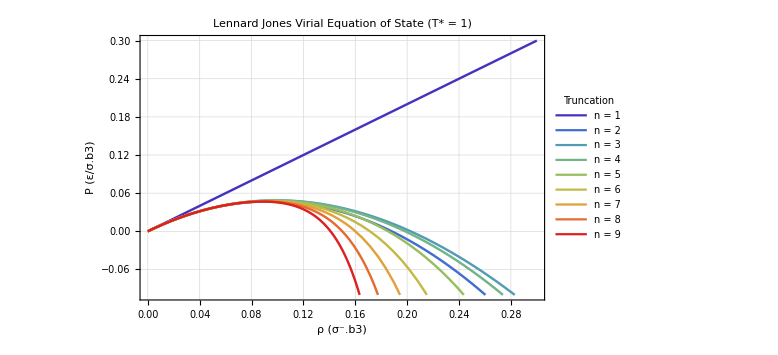

```mathematica
colors=ColorData["Rainbow"][#/9]&/@Range[1,9];

Plot[Evaluate@Table[P[ρ,n],{n,1,9}],{ρ,0,0.3},PlotStyle->(Directive[#,Thickness[0.003]]&/@colors),PlotLegends->Placed[LineLegend[colors,Table["n = "<>ToString[n],{n,1,9}],LegendLabel->"Truncation",LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->GrayLevel[0.7]]&),LabelStyle->Directive[FontFamily->"Times",FontSize->12]],After],PlotLabel->Style["Lennard Jones Virial Equation of State (T* = 1)",FontFamily->"Times",FontSize->16,Bold,Black],PlotRange->{-0.1,0.3},Frame->True,FrameLabel->{Style["ρ  (σ⁻.b3)",FontFamily->"Times",FontSize->14],Style["P  (ε/σ.b3)",FontFamily->"Times",FontSize->14]},FrameStyle->Directive[Black,Thickness[0.002]],GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->Large,Background->White,PlotRangePadding->{{0,Automatic},{Automatic,Automatic}}]
```